## Numerical Results for Neutrino Oscillations in Matter

### Prep

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/code

### Numerical

First of all I need to construct the function of solar electron number density.

```mathematica
numDenListRaw=Import["data/neordered.txt","Table"]
```

{{0.00819005,2.00852},{0.00831693,2.00847},{0.00844579,2.00842},{0.00857666,2.00837},{0.00870957,2.00832},{0.00884456,2.00826},{0.00898165,2.0082},{0.00912087,2.00814},{0.00926227,2.00808},{0.00940589,2.00802},{0.00955174,2.00795},{0.00969987,2.00788},2475,{1.00132,-9.86034},{1.00132,-9.86737},{1.00133,-9.87444},{1.00133,-9.88157},{1.00133,-9.88876},{1.00133,-9.896},{1.00134,-9.9033},{1.00134,-9.91065},{1.00134,-9.91807},{1.00135,-9.92555},{1.00135,-9.9331},{1.00135,-9.94071}}
 |  |  |  |

#### Remove the duplicates

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```

into 2 lists

```mathematica
numDenListRaw1=Table[numDenListRaw[[i]][[1]],{i,1,Length@numDenListRaw}];
numDenListRaw2=Table[numDenListRaw[[i]][[2]],{i,1,Length@numDenListRaw}];
```

```mathematica
Length@numDenListRaw1 - Length@numDenListRaw2
```

0

```mathematica
dupPosNumDenListRaw1=positionDuplicates[numDenListRaw1];
```

```mathematica
dupPosNumDenListRaw1C=Flatten@Table[Delete[dupPosNumDenListRaw1[[i]],1],{i,1,Length@dupPosNumDenListRaw1}];
```

```mathematica
dupPosNumDenListRaw1CD=Table[{dupPosNumDenListRaw1C[[i]]},{i,1,Length@dupPosNumDenListRaw1C}];
```

```mathematica
numDenListRaw1D=Delete[numDenListRaw1,dupPosNumDenListRaw1CD];
numDenListRaw2D=Delete[numDenListRaw2,dupPosNumDenListRaw1CD];
```

```mathematica
Length@numDenListRaw1D-Length@numDenListRaw2D
```

0

```mathematica
numDenList=Partition[Riffle[numDenListRaw1D,numDenListRaw2D],2]
```

{{0.00819005,2.00852},{0.00831693,2.00847},{0.00844579,2.00842},{0.00857666,2.00837},{0.00870957,2.00832},{0.00884456,2.00826},{0.00898165,2.0082},{0.00912087,2.00814},{0.00926227,2.00808},{0.00940589,2.00802},{0.00955174,2.00795},{0.00969987,2.00788},1875,{1.00125,-9.68062},{1.00126,-9.70463},{1.00127,-9.72911},{1.00128,-9.75412},{1.00129,-9.77969},{1.0013,-9.80588},{1.00131,-9.82596},{1.00132,-9.85337},{1.00133,-9.87444},{1.00134,-9.9033},{1.00135,-9.92555}}
 |  |  |  |

```mathematica
First@numDenList
Last@numDenList
```

{0.00819005,2.00852}

{1.00135,-9.92555}

#### Define Interpolation Function

```mathematica
numDen=Interpolation[numDenList]
```

InterpolatingFunction[{{0.00819005, 1.00135}}, <>]

```mathematica
numDen[1.0]
```

-6.80567

```mathematica
numDenDeri[x_]=D[numDen[x],x]
```

InterpolatingFunction[{{0.00819005, 1.00135}}, <>][x]

```mathematica
numDenDeri[0.5]
```

-4.44152

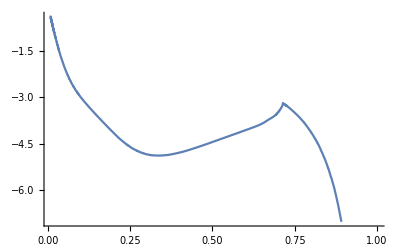

```mathematica
Plot[numDenDeri[x],{x,0.00819005,1.00135}]
```

The Hamiltonian becomes

```mathematica
omegam[energy_]=deltam^2/(4 energy)
```

deltam^2/(4 energy)

Fermi coupling constant G_F /(hbar c)    1.166 378 7(6)×10^−5 GeV−2

```mathematica
deltaH=1
thetaV=Pi/6
omegaMatter=10^(-6)
rSun=695800000
```

1

π/6

1/1000000

695800000

```mathematica
nDeri[x_]=1.41*1.17*10^(-5)*numDenDeri[x]
```

0.000016497 InterpolatingFunction[{{0.00819005, 1.00135}}, <>][x]

```mathematica
omegaMatter{{- Sqrt[(deltaH^2+1)/4-deltaH Cos[2thetaV]/2],0},{0, Sqrt[(deltaH^2+1)/4-deltaH Cos[2thetaV]/2]}}
```

{{-1/2000000,0},{0,1/2000000}}

```mathematica
hamilD[x_]=omegaMatter{{- Sqrt[(deltaH^2+1)/4-deltaH Cos[2thetaV]/2],0},{0, Sqrt[(deltaH^2+1)/4-deltaH Cos[2thetaV]/2]}}-I nDeri[x] Sin[thetaV]Cos[thetaV]{{0,1},{-1,0}} 
%//MatrixForm
```

{{-5.×10^-7+0. ⅈ,(0.-7.14341×10^-6 ⅈ) InterpolatingFunction[{{0.00819005, 1.00135}}, <>][x]},{(0.+7.14341×10^-6 ⅈ) InterpolatingFunction[{{0.00819005, 1.00135}}, <>][x],5.×10^-7+0. ⅈ}}

(-5.×10^-7+0. ⅈ | (0.-7.14341×10^-6 ⅈ) InterpolatingFunction[{{0.00819005, 1.00135}}, <>][x]
(0.+7.14341×10^-6 ⅈ) InterpolatingFunction[{{0.00819005, 1.00135}}, <>][x] | 5.×10^-7+0. ⅈ)

```mathematica
hamilD[0.5]
%//MatrixForm
```

{{-5.×10^-7+0. ⅈ,0.+0.0000317276 ⅈ},{0.-0.0000317276 ⅈ,5.×10^-7+0. ⅈ}}

(-5.×10^-7+0. ⅈ | 0.+0.0000317276 ⅈ
0.-0.0000317276 ⅈ | 5.×10^-7+0. ⅈ)

The function to be obtained is

```mathematica
nuM[x_]={nuML[x],nuMH[x]}
```

{nuML[x],nuMH[x]}

The system becomes

```mathematica
matOsc=I nuM'[x]==hamilD[x].nuM[x]
```

{ⅈ nuML'[x],ⅈ nuMH'[x]}=={(-5.×10^-7+0. ⅈ) nuML[x]-(0.+7.14341×10^-6 ⅈ) nuMH[x] InterpolatingFunction[{{0.00819005, 1.00135}}, <>][x],(5.×10^-7+0. ⅈ) nuMH[x]+(0.+7.14341×10^-6 ⅈ) nuML[x] InterpolatingFunction[{{0.00819005, 1.00135}}, <>][x]}

```mathematica
solM=NDSolve[matOsc&&nuM[0]=={1,0},{nuML,nuMH},x]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{nuML→InterpolatingFunction[{{0., 0.}}, <>],nuMH→InterpolatingFunction[{{0., 0.}}, <>]}}

```mathematica
probsqrt=nuML/.solM[[1]]
```

InterpolatingFunction[{{0., 0.}}, <>]

```mathematica
probsqrt[0.2]
```

InterpolatingFunction::dmval: Input value {0.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.+1.×10^-7 ⅈ

InterpolatingFunction::dmval: Input value {0.100018} lies outside the range of data in the interpolating function. Extrapolation will be used.

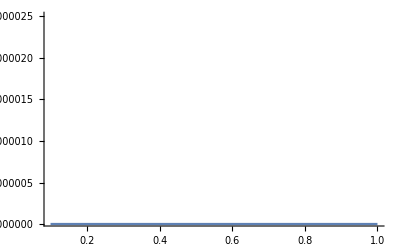

```mathematica
Plot[Abs[probsqrt[x]]^2,{x,0.1,1}]
```

```mathematica
Abs[probsqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 0.}}, <>][x]]^2